## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## longest times when τα belongs (1000,10000)

### check if we equilibrate long enough

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031 ,0.0028, 0.0025 ,0.0022 ,0.002 ,0.0018,0.001 ,0.00067, 0.0005 ,0.0004, 0.00033,0.00025 ,0.00018 ,0.00014 ,0.00011 ,0.0001};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000,0.00025000,0.00018000,0.00014000,0.00011000,0.00010000}

```mathematica
wtlist={0.,80000.,90000.,100000.};
```

```mathematica
wtlist={0.,50000.,60000.,70000.,80000.,90000.,100000.};
```

```mathematica
wtliststring=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlist
```

{0.00,80000.00,90000.00,100000.00}

```mathematica
wtlistLongest={10000.,10000.,10000.,10000.,10000.,10000.,10000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.};
```

```mathematica
wtlistLongestString=ToString[NumberForm[#,{9,2},ExponentFunction->(Null&)]]&/@wtlistLongest
```

{10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,10000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00,100000.00}

```mathematica
SISF=Table[Table[Import[StringJoin[saveFolder,"SISFCRSISF_N4096_p3.8500_T",Tstring[[Length[Tlist]-1]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,2}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/SISFCRSISF_N4096_p3.8500_T0.00011000_waitingTime50000.00_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/SISFCRSISF_N4096_p3.8500_T0.00011000_waitingTime60000.00_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/SISFCRSISF_N4096_p3.8500_T0.00011000_waitingTime70000.00_idx0.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
overlap=Table[Table[Import[StringJoin[saveFolder,"overlapCRoverlap_N4096_p3.8500_T",Tstring[[16]],"_waitingTime",wtliststring[[wt]],"_idx",ToString[idx],".nc"],"Data"],{wt,Length[wtlist]}],{idx,0,2}];
```

```mathematica
timeLongest=Table[testdata=Import[StringJoin[saveFolder,"glassyDynamics_N4096_p3.8500_T",Tstring[[16]],"_waitingTime",wtliststring[[wt]],"_idx1.nc"],"Data"];Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}],{wt,Length[wtlist]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/glassyDynamics_N4096_p3.8500_T0.00180000_waitingTime0.00_idx1.nc not found during Import.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦4,1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/glassyDynamics_N4096_p3.8500_T0.00180000_waitingTime50000.00_idx1.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/glassyDynamics_N4096_p3.8500_T0.00180000_waitingTime60000.00_idx1.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
CRFswaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[SISF[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-5}],{wt,Length[wtlist]}],FrameLabel->{"time","CRFs"},ImageSize->600,PlotLabel->"CRFs vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,Length[wtlist]}],PlotRange->All]
```

-Graphics-

```mathematica
CRoverlapwaitTime=ListLogLinearPlot[Table[Table[{timeLongest[[wt,t]],Mean[Table[overlap[[idx,wt,2,t]],{idx,3}]]},{t,Length[timeLongest[[wt]]]-5}],{wt,4}],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True,PlotStyle->redBluePlotConfig[7],PlotLegends->Table["waitingtime="<>ToString[wtlist[[wt]]],{wt,4}],PlotRange->{All,{0,1}}]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlapwaitTimeLT.jpeg",CRoverlapwaitTimeLT,ImageResolution->600];
```

### the relaxation time for these low temperature

```mathematica
overlap=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/overlapCRoverlap_N4096_p3.8500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
Length[Tlist]
```

26

```mathematica
SISF=Table[Table[Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p385/SISFCRSISF_N4096_p3.8500_T",Tstring[[T]],"_waitingTime",wtlistLongestString[[T]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
CRoverlapMean=Table[Table[Mean[Table[overlap[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
overlapMean=Table[Table[Mean[Table[overlap[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
CRSISFMean=Table[Table[Mean[Table[SISF[[T,i,2,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
SISFMean=Table[Table[Mean[Table[SISF[[T,i,1,rec]],{i,3}]],{rec,Min[Length[overlap[[T,1,1]]],Length[overlap[[T,2,1]]],Length[overlap[[T,3,1]]]]}],{T,Length[Tlist]}];
```

```mathematica
testdata=Import[StringJoin["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p385/glassyDynamics_N4096_p3.8500_T",Tstring[[Length[Tlist]]],"_waitingTime",wtlistLongestString[[Length[Tlist]]],"_idx1.nc"],"Data"];time=Table[testdata[[4,j,1]]-testdata[[4,1,1]],{j,Length[testdata[[4]]]}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

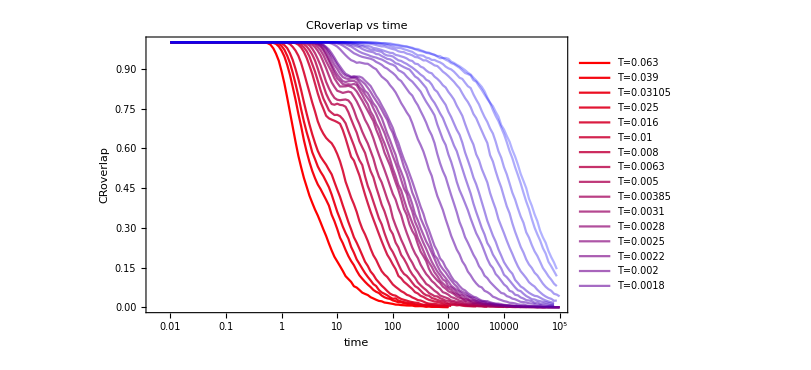

```mathematica
CRoverlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time",Joined->True]
```

```mathematica
fitCROverlapStartNum={4.545633497156052,6.972324797990245,7.688430481846143,9.342191365655887,11.359328382212755,15.816075884439703,17.103424454731552,21.189518319840886,23.81560922495133,27.8367722375015,30.685453336137705,33.82312067339929,36.55834456391838,39.51772229179588,41.89421685655501,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,46.16936129187266,80.,80.,80.,80.,80.};
```

```mathematica
fitCROverlapStartPos=Table[Position[time,_?(#>fitCROverlapStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70}

```mathematica
fitsCROverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[T,rec]]]},{rec,fitCROverlapStartPos[[T]],Length[CRoverlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

```mathematica
fitsCROverlap
```

{FittedModel[0.999939 ⅇ^(-0.515545 t^0.519302)],FittedModel[0.999966 ⅇ^(-0.353184 t^0.541758)],FittedModel[0.999971 ⅇ^(-0.2793 t^0.568154)],FittedModel[0.999978 ⅇ^(-0.222379 t^0.586029)],FittedModel[0.999987 ⅇ^(-0.161697 t^0.593373)],FittedModel[0.999993 ⅇ^(-0.0907881 t^0.646466)],FittedModel[0.999995 ⅇ^(-0.0756969 t^0.649911)],FittedModel[0.999995 ⅇ^(-0.0587052 t^0.661151)],FittedModel[0.999996 ⅇ^(-0.0469572 t^0.66898)],FittedModel[0.999996 ⅇ^(-0.0360893 t^0.677554)],FittedModel[0.999997 ⅇ^(-0.0279403 t^0.691862)],FittedModel[0.999998 ⅇ^(-0.0266328 t^0.686269)],FittedModel[0.999998 ⅇ^(-0.0223404 t^0.698644)],FittedModel[0.999998 ⅇ^(-0.0206731 t^0.696748)],FittedModel[0.999998 ⅇ^(-0.0162701 t^0.717823)],FittedModel[0.999998 ⅇ^(-0.0162733 t^0.701715)],FittedModel[0.999999 ⅇ^(-0.00704847 t^0.736315)],FittedModel[0.999999 ⅇ^(-0.00444992 t^0.741402)],FittedModel[0.999999 ⅇ^(-0.00353361 t^0.725584)],FittedModel[0.999999 ⅇ^(-0.00267254 t^0.729492)],FittedModel[0.999999 ⅇ^(-0.00188821 t^0.741303)],FittedModel[0.999999 ⅇ^(-0.0014236 t^0.733621)],FittedModel[0.999998 ⅇ^(-0.000814249 t^0.752556)],FittedModel[0.999999 ⅇ^(-0.000641544 t^0.743966)],FittedModel[0.999995 ⅇ^(-0.000330518 t^0.778901)],FittedModel[0.999998 ⅇ^(-0.000380123 t^0.754086)]}

```mathematica
tauCROverlapfits=Table[fitsCROverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{3.5816,6.82841,9.43977,13.0053,21.5555,40.9069,53.0556,72.844,96.7288,134.636,176.108,196.975,230.685,261.696,310.253,353.828,836.628,1485.58,2393.55,3366.77,4726.53,7589.61,12735.1,19568.5,29435.,34307.9}

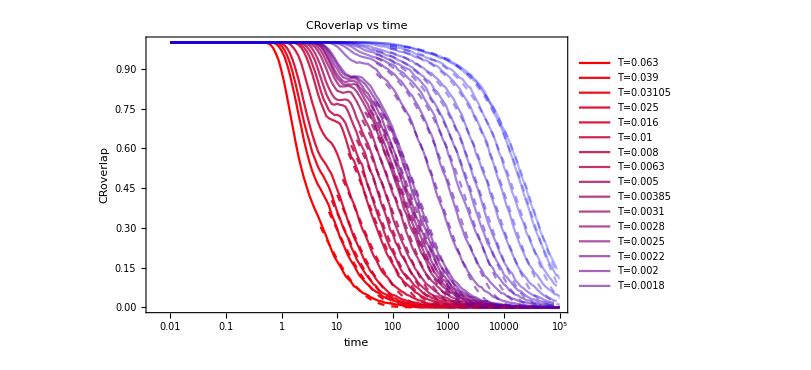

```mathematica
Show[CRoverlapPlot,Table[LogLinearPlot[fitsCROverlap[[T]][x],{x,time[[fitCROverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

### overlap

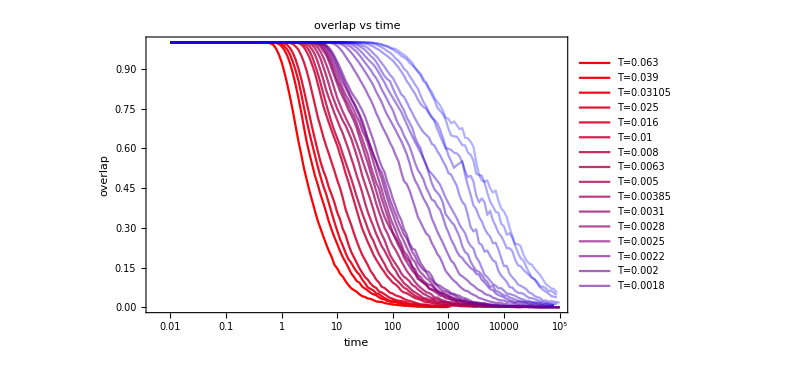

```mathematica
overlapPlot=ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[T,rec]]},{rec,Length[CRoverlapMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time",Joined->True]
```

```mathematica
Log10[time[[66]]]
```

Part::partw: Part 66 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

Log[{0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧}⟦66⟧]/Log[10]

```mathematica
fitOverlapStartPos=fitCROverlapStartPos+8
```

{53,56,57,59,61,63,64,66,67,68,69,70,71,71,72,73,73,73,73,73,73,78,78,78,78,78}

```mathematica
{45,48,49,51,53,55,56,58,59,60,61,62,63,63,64,65,65,65,65,65,65,70,70,70,70,70}-10
```

{35,38,39,41,43,45,46,48,49,50,51,52,53,53,54,55,55,55,55,55,55,60,60,60,60,60}

```mathematica
fitsOverlap=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[T,rec]]]},{rec,fitOverlapStartPos[[T]],Length[overlapMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,1.0>G>0,τ>0.5}},{G,τ,β,c},t],{T,Length[Tlist]}];
```

```mathematica
fitsOverlap
```

{FittedModel[0.998925 ⅇ^(-0.880722 t^0.370944)],FittedModel[0.99906 ⅇ^(-0.730777 t^0.367725)],FittedModel[0.999463 ⅇ^(-0.567867 t^0.411633)],FittedModel[0.999372 ⅇ^(-0.562359 t^0.390148)],FittedModel[0.999676 ⅇ^(-0.414012 t^0.425282)],FittedModel[0.999793 ⅇ^(-0.327558 t^0.423669)],FittedModel[0.999869 ⅇ^(-0.273158 t^0.440648)],FittedModel[0.999878 ⅇ^(-0.216337 t^0.465497)],FittedModel[0.999909 ⅇ^(-0.208124 t^0.452783)],FittedModel[0.999913 ⅇ^(-0.159898 t^0.479894)],FittedModel[0.999919 ⅇ^(-0.155677 t^0.458633)],FittedModel[0.99995 ⅇ^(-0.174383 t^0.439364)],FittedModel[0.999951 ⅇ^(-0.157876 t^0.446567)],FittedModel[0.999958 ⅇ^(-0.124417 t^0.476096)],FittedModel[0.999958 ⅇ^(-0.124152 t^0.463107)],FittedModel[0.999963 ⅇ^(-0.123782 t^0.455133)],FittedModel[0.99999 ⅇ^(-0.0492038 t^0.537099)],FittedModel[0.999996 ⅇ^(-0.0321897 t^0.560408)],FittedModel[0.999997 ⅇ^(-0.0361792 t^0.507843)],FittedModel[0.999998 ⅇ^(-0.0228716 t^0.551049)],FittedModel[0.999998 ⅇ^(-0.0248507 t^0.521444)],FittedModel[0.999988 ⅇ^(-0.0200756 t^0.510676)],FittedModel[0.999997 ⅇ^(-0.0114285 t^0.548515)],FittedModel[0.999999 ⅇ^(-0.0183021 t^0.468515)],FittedModel[0.999999 ⅇ^(-0.00865112 t^0.533056)],FittedModel[0.999999 ⅇ^(-0.00841239 t^0.523173)]}

```mathematica
tauOverlapfits=Table[fitsOverlap[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

{1.40833,2.34653,3.95386,4.37269,7.95333,13.9341,19.0105,26.8103,32.028,45.6069,57.712,53.2539,62.4043,79.6394,90.4598,98.5318,272.464,460.1,689.534,949.332,1194.93,2107.15,3471.29,5111.19,7413.19,9254.09}

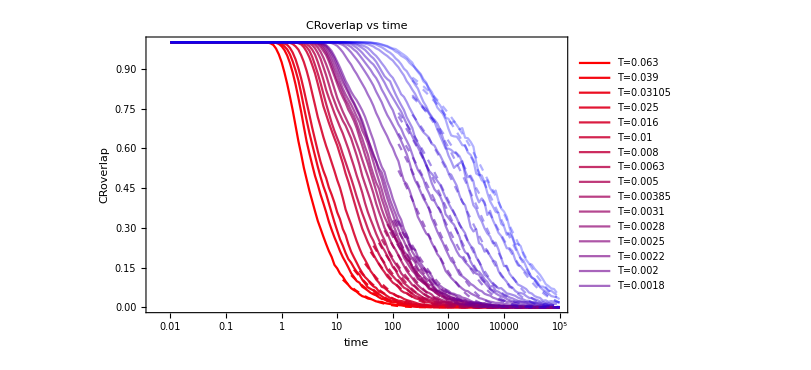

```mathematica
Show[overlapPlot,Table[LogLinearPlot[fitsOverlap[[T]][x],{x,time[[fitOverlapStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

```mathematica
Export["/home/chengling/Research/updates/02012024/CRoverlap.jpeg",Show[CRoverlapfitST,CRoverlapLTPlot,Table[LogLinearPlot[fitsCRoverlapLT[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]+Length[TlistLT]][[T+Length[Tlist]]]}],{T,Length[TlistLT]}]],ImageResolution->600];
```

Show::gcomb: Could not combine the graphics objects in Show[CRoverlapfitST,CRoverlapLTPlot,{}].

#### CRSISF

Part::partw: Part 3 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

Part::partw: Part 4 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

Part::partw: Part 5 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

-Graphics-

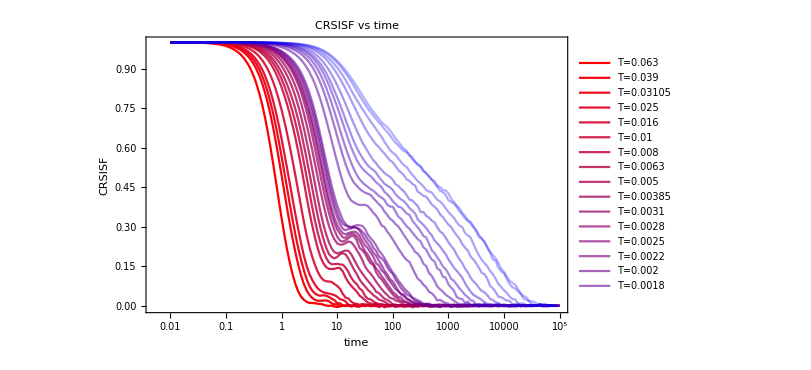

-Graphics-

```mathematica
CRSISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[T,rec]]},{rec,Length[CRSISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","CRSISF"},ImageSize->600,PlotLabel->"CRSISF vs time",Joined->True]
```

```mathematica
fitCRSISFStartNum={4.337072420050368,7.194205862609111,7.931187148870541,11.041221920722247,12.41437888222547,15.092266119370647,17.301989581024966,20.62319820061897,23.639957937652536,28.730316073927884,33.577461003101725,36.300996533057514,40.01970511999825,41.61110332104524,46.77333136987734,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,51.55879183196962,80.,80.,80.,80.,80.};
```

```mathematica
fitCRSISFStartPos=Table[Position[time,_?(#>fitCRSISFStartNum[[i]]&)][[1,1]],{i,Length[Tlist]}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧,{}⟦1,1⟧}

```mathematica
fitsCRSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[T,rec]]]},{rec,fitCRSISFStartPos[[T]],Length[CRSISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

Table::iterb: Iterator {rec,{}⟦1,1⟧,91} does not have appropriate bounds.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

Table::iterb: Iterator {rec,{}⟦1,1⟧,91} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

```mathematica
fitsCRSISF
```

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

{NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,92}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,101}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,105}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,111}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,117}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,126}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t]}

```mathematica
tauCRSISFfits=Table[fitsCRSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

Table::iterb: Iterator {rec,{}⟦1,1⟧,91} does not have appropriate bounds.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

Table::iterb: Iterator {rec,{}⟦1,1⟧,91} does not have appropriate bounds.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

Table::iterb: Iterator {rec,{}⟦1,1⟧,91} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t Power[«2»])^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,92}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,101}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,105}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,111}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,117}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,126}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧}

```mathematica
Length[TlistLongest]
```

0

```mathematica
Show[CRSISFPlot,Table[LogLinearPlot[fitsCRSISF[[T]][x],{x,fitCRSISFStartNum[[T]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[CRSISFMean⟦T,rec⟧]},{rec,{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Table::iterb: Iterator {rec,{}⟦1,1⟧,91.} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/CRSISF_p380.jpeg",Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,Table[LogLinearPlot[fitsCRSISFLongest[[T]][x],{x,timeLT[[52]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[TlistAllT]][[T+Length[Tlist]+Length[TlistLT]]]}],{T,Length[TlistLongest]}]]];
```

Show::gcomb: Could not combine the graphics objects in Show[CRSISFSTLTwithFitPlot,CRSISFLongestPlot,{}].

#### SISF

```mathematica
SISFPlot=ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[T,rec]]},{rec,Length[SISFMean[[T]]]}],{T,Length[Tlist]}],PlotLegends->Table["T="<>ToString[Tlist[[T]]],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[Length[Tlist]],FrameLabel->{"time","SISF"},ImageSize->600,PlotLabel->"SISF vs time",Joined->True]
```

Part::partw: Part 3 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

Part::partw: Part 4 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

Part::partw: Part 5 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
time[[40]]
```

Part::partw: Part 40 of {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧} does not exist.

{0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧}⟦40⟧

```mathematica
fitSISFStartPos=fitCRSISFStartPos-5
```

{-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧,-5+{}⟦1,1⟧}

```mathematica
fitsSISF=Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[T,rec]]]},{rec,fitSISFStartPos[[T]],Length[SISFMean[[T]]]}],{stretchedExp[t,G,τ,β],{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],{T,Length[Tlist]}];
```

Table::iterb: Iterator {rec,-5+{}⟦1,1⟧,91} does not have appropriate bounds.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

Table::iterb: Iterator {rec,-5+{}⟦1,1⟧,91} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

```mathematica
fitsSISF
```

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

{NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,92}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,101}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,105}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,111}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,117}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,126}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t],NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t]}

```mathematica
tauSISFfits=Table[fitsSISF[[T]]["BestFitParameters"][[2,2]],{T,Length[Tlist]}]
```

Table::iterb: Iterator {rec,-5+{}⟦1,1⟧,91} does not have appropriate bounds.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

Table::iterb: Iterator {rec,-5+{}⟦1,1⟧,91} does not have appropriate bounds.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

Table::iterb: Iterator {rec,-5+{}⟦1,1⟧,91} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t Power[«2»])^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,91}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,92}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,101}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,105}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,111}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,117}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,126}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,129}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,131}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[Table[{Normal[time⟦rec⟧],Normal[SISFMean⟦T,rec⟧]},{rec,-5+{}⟦1,1⟧,130}],{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧}

```mathematica
Show[SISFPlot,Table[LogLinearPlot[fitsSISF[[T]][x],{x,time[[fitSISFStartPos[[T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[Tlist]][[T]]}],{T,Length[Tlist]}]]
```

Part::pkspec1: The expression -5+{}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value {0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧}⟦-5+{}⟦1,1⟧⟧ in {x,{0,-$Failed⟦4,1,1⟧+$Failed⟦4,2,1⟧}⟦-5+{}⟦1,1⟧⟧,100000} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

$Aborted

#### Tau Alphas

```mathematica
tauAlphafitingPlot=ListLogPlot[{Table[{1/Tlist[[T]],tauCROverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauCRSISFfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauOverlapfits[[T]]},{T,Length[Tlist]}],Table[{1/Tlist[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■"],Style["●"],Style["□"],Style["○"]},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->{{0,15000},All}]
```

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of NonlinearModelFit[{},{2.718281828459045^(-1. (t Power[«2»])^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

Part::partw: Part 2 of NonlinearModelFit[{},{2.718281828459045^(-1. (t Power[«2»])^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Part::partw: Part 2 of NonlinearModelFit[{},{2.718281828459045^(-1. (t Power[«2»])^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
tauTable=Prepend[Table[{Tlist[[T]],tauCRSISFfits[[T]],tauCROverlapfits[[T]],tauOverlapfits[[T]],tauSISFfits[[T]]},{T,Length[Tlist]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}]
```

{{T,τα CRSISF,τα CR overlap,τα SISF,τα overlap},{0.063,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.039,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.03105,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.025,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.016,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.01,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.008,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0063,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.005,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00385,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0031,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0028,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0025,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0022,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.002,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0018,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.001,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00067,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0005,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0004,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00033,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00025,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00018,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00014,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.00011,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧},{0.0001,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.99>β>0.2,1.>G>0,τ>0.5}},{G,τ,β,c},t][BestFitParameters]⟦2,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,1>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦2,2⟧}}

```mathematica
N[Table[1/(i*1000+10000),{i,1,5}]]
```

{0.0000909091,0.0000833333,0.0000769231,0.0000714286,0.0000666667}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP385.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP385.csv

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha_p385.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
Export["/home/chengling/Research/updates/02012024/taualpha.jpeg",tauAlphafitingPlot,ImageResolution->600];
```

```mathematica
betaCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

Part::partw: Part 3 of NonlinearModelFit[{},{ⅇ^(-(t Power[«2»])^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦3,2⟧}

```mathematica
GCRSISFfitsAllT=Join[Table[fitsCRSISF[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRSISFLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRSISFLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification NonlinearModelFit[{},{ⅇ^(-Times[«2»]^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧,NonlinearModelFit[{},{ⅇ^(-(t/τ)^β) G,{0.9>β>0.2,0.6>G>0,τ>0.5}},{G,τ,β},t][BestFitParameters]⟦1,2⟧}

```mathematica
betaCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[3,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[3,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification fitsCRoverlap⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of fitsCRoverlap⟦1⟧[BestFitParameters] does not exist.

Part::partd: Part specification fitsCRoverlap⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of fitsCRoverlap⟦2⟧[BestFitParameters] does not exist.

Part::partd: Part specification fitsCRoverlap⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of fitsCRoverlap⟦3⟧[BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{fitsCRoverlap⟦1⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦2⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦3⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦4⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦5⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦6⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦7⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦8⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦9⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦10⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦11⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦12⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦13⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦14⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦15⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦16⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦17⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦18⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦19⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦20⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦21⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦22⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦23⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦24⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦25⟧[BestFitParameters]⟦3,2⟧,fitsCRoverlap⟦26⟧[BestFitParameters]⟦3,2⟧}

```mathematica
GCRoverlapfitsAllT=Join[Table[fitsCRoverlap[[T]]["BestFitParameters"][[1,2]],{T,Length[Tlist]}],Table[fitsCRoverlapLT[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLT]}],Table[fitsCRoverlapLongest[[T]]["BestFitParameters"][[1,2]],{T,Length[TlistLongest]}]]
```

Part::partd: Part specification fitsCRoverlap⟦1⟧ is longer than depth of object.

Part::partd: Part specification fitsCRoverlap⟦1⟧[BestFitParameters]⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification fitsCRoverlap⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{fitsCRoverlap⟦1⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦2⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦3⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦4⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦5⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦6⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦7⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦8⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦9⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦10⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦11⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦12⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦13⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦14⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦15⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦16⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦17⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦18⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦19⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦20⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦21⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦22⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦23⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦24⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦25⟧[BestFitParameters]⟦1,2⟧,fitsCRoverlap⟦26⟧[BestFitParameters]⟦1,2⟧}

```mathematica
betafitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],betaCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],betaCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","β"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"β vs 1/T",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingBeta_p380_p380.jpeg",betafitingPlot,ImageResolution->600];
```

```mathematica
GfitingPlot=ListLogPlot[{Table[{1/TlistAllT[[T]],GCRoverlapfitsAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],GCRSISFfitsAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","A"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"A vs 1/T",Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/fittingA_p380_p380.jpeg",GfitingPlot,ImageResolution->600];
```

```mathematica
tauCRSISFAllT
```

tauCRSISFAllT

```mathematica
tauTable=Prepend[Table[{TlistAllT[[T]],tauCRSISFAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],{"T","τα CRSISF","τα CR overlap"}]
```

{{T,τα CRSISF,τα CR overlap}}

```mathematica
Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv",tauTable,"CSV"]
```

/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlphaTableP380.csv

```mathematica
NumberForm[#,{9,6},ExponentFunction->(Null&)]&/@TlistAllT
```

TlistAllT

```mathematica
TlistAllT
```

TlistAllT

```mathematica
TlistGeneral={0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}
```

{0.063,0.039,0.03105,0.025,0.016,0.01,0.008,0.0063,0.005,0.00385,0.0031,0.28,0.0025,0.0022,0.002,0.0018}

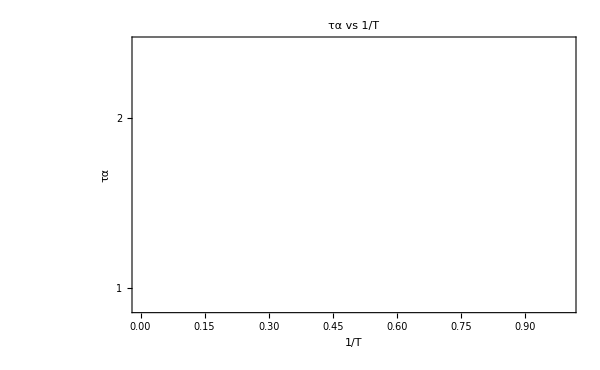

```mathematica
ListLogPlot[{Table[{1/TlistAllT[[T]],tauCRoverlapAllT[[T]]},{T,Length[TlistAllT]}],Table[{1/TlistAllT[[T]],tauCRSISFAllT[[T]]},{T,Length[TlistAllT]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF"},PlotMarkers->{Automatic},ImageSize->600,PlotLabel->"τα vs 1/T",Joined->True,PlotRange->All,Epilog->Table[Line[{{1/TlistGeneral[[T]],0},{1/TlistGeneral[[T]],10000}}],{T,Length[TlistGeneral]}]]
```

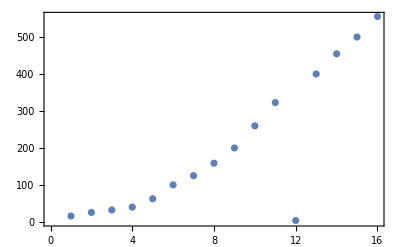

```mathematica
ListPlot[1/TlistGeneral]
```

```mathematica
tauEsGeneral={1.1841166706949628,2.462846296611076,3.8650575360708697,5.57413355409462,11.924841063370899,33.8105307104969,54.5761704083136,107.2953843344434,216.96587756816794,565.3189946945129,1243.945127271425,2065.,3731.3453237234366,7000.,12885.217184405017,22000.};
```

```mathematica
Length[TlistGeneral]
```

16